```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/lederstrumpf/Development_Dirty_Playground/Casper/p2pvoting/gif_processing

## Chain traversing

```mathematica
prevblock[data_]:=data["prevblock"]
prevblockIter[data_,depth_]:=Nest[prevblock,data,depth]
sender[data_]:=data["sender"]
prevblockSender[data_,depth_]:=sender@prevblockIter[data,depth]
```

## Clique Signalling Circle

```mathematica
SelectLargestGroup[cliques_,id_]:=Select[cliques,MemberQ[#,ToString@id]&]
Clear@CircleInCliqueCheap;
CircleInCliqueCheap[frame_,totalFrames_,cliques_,viewingValidator_,supercliques_,{xc_,yc_},radius_]:=Module[{validator=xc},
(*Print@cliques;
CliquesSegregated=SelectLargestGroup[cliques,#]&/@Range@Length@cliques;
Print@CliquesSegregated;
Cliques=Apply[Join,SelectLargestGroup[cliques,#]&/@Range@Length@cliques]//DeleteDuplicates;
Print@Cliques;
CliqueColorMap=Cliques[[#]]->ColorData[24][#]&/@Range@Length@Cliques;
Print@CliqueColorMap;
KeysOfValidator=Select[Keys@CliqueColorMap,MemberQ[#,ToString@validator]&];
Print@KeysOfValidator;
Args={KeysOfValidator[[#]]/.CliqueColorMap,Disk[{xc,yc},radius,{(#-1) (2π)/(Length@KeysOfValidator),(#) (2π)/(Length@KeysOfValidator)}]}&/@Range@Length@KeysOfValidator;
Print@Length@Args;
If[Length@Args== 0,{Purple,Disk[{xc,yc},radius]},Join@@Args]*)
(*Print@{viewingValidator,validator};*)
If[frame==totalFrames
∧Intersection[supercliques,cliques]≠{}
∧MemberQ[MaximalBy[cliques,Length]//First,ToString@validator]
(*∧viewingValidator == validator*),
{Red,Disk[{xc,yc},radius]},
If[viewingValidator==validator+1,
{Green,Disk[{xc,yc},radius]},
{Gray,Disk[{xc,yc},radius]}]
(*{Gray,Disk[{xc,yc},radius]}*)
]
]
```

## Circle Function

```mathematica
Clear[CircleFnCheap]
Clear[CircleCurriedCheap]
CircleFnCheap[frame_,totalFrames_,cliques_,viewingValidator_,supercliques_,{xc_,yc_},name_,{w_,h_}]:=Module[{},
(*Print@{xc,yc};*)
(*Print@{name};
Print@{w,h};*)
(*Print@CircleInClique[frame,IntegerPart[xc]];*)
(*CircleInClique[frame,IntegerPart[xc]]*)
(*Disk[{xc,yc},1.0]*)
CircleInCliqueCheap[frame,totalFrames,cliques,viewingValidator,supercliques,{IntegerPart@xc,yc},0.2]
]
CircleCurriedCheap[frame_,totalFrames_,cliques_,viewingValidator_,supercliques_]:=Function[{a,b,c}, CircleFnCheap[frame,totalFrames,cliques,viewingValidator,supercliques,a,b,c]]
```

## Arrowhead

```mathematica
ScalingFactor=4;
ℛ=Triangle[{{0,-ScalingFactor},{0,ScalingFactor},{-ScalingFactor,0}}];
Hed=Graphics[{Red,ℛ}];
ef[pts_List,e_]:=
Block[{s=0.015,g=Hed},{Arrowheads[{{s,0.5,g}}],Arrow[pts]}]
```

## Data Processing (legacy)

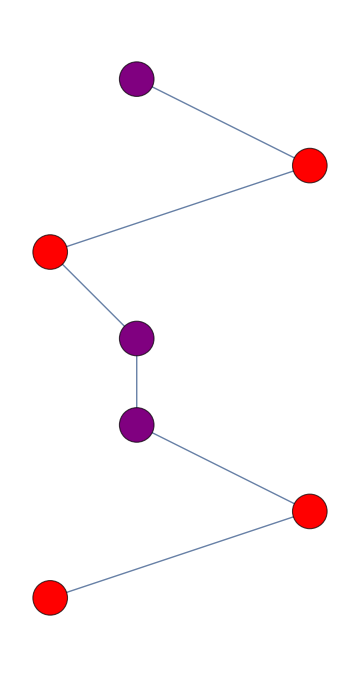

```mathematica
Table[Module[{index=i},
Dit=Drt[[index]]//Reverse;
Dyt={ToExpression@Dit[[#]],#}&/@Range@Length@Dit;
Dut=Dyt[[#,2]]->Dyt[[#+1,2]]&/@Range[-1+Length@Dyt];
DitFinal=Drt[[-1]]//Reverse;
DytFinal={ToExpression@DitFinal[[#]],#}&/@Range@Length@DitFinal;
DutFinal=DytFinal[[#,2]]->DytFinal[[#+1,2]]&/@Range[-1+Length@DytFinal];
Show[
Graph[
DutFinal,
VertexCoordinates->DytFinal,
EdgeShapeFunction->GraphElementData["CarvedArrow","ArrowSize"->Medium],
VertexStyle->White,
EdgeStyle->White,
BaseStyle->EdgeForm[None],
GraphHighlightStyle->"DehighlightHide",
ImageSize->Medium],
Graph[
Dut,
VertexCoordinates->Dyt,
EdgeShapeFunction->ef,
(*VertexLabels->Automatic,*)
(*VertexStyle->Red,*)
VertexShapeFunction-> CircleCurriedCheap[i,Length@Drt,Data[[i]]["clqs"][[1]]],
VertexSize->0.25,
EdgeStyle->Thick]]
(*,Data[[i]]["clqs"][[1]]*)],{i,Length@Drt}][[-1]]
(*Export["stuff.gif",%]*)
```

{0.,1.}

1

{1.,2.}

3

{1.,3.}

3

{1.,4.}

3

{0.,5.}

1

{1.,6.}

3

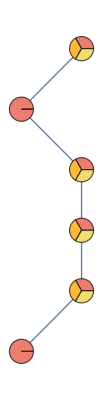

```mathematica
Graph[
Dut,
VertexCoordinates->Dyt,
EdgeShapeFunction->ef,
(*VertexStyle->Red,*)
VertexShapeFunction-> CircleCurried[5],
VertexSize->0.25,
EdgeStyle->Thick]
```

## Data Processing Some Receivers

```mathematica
sequenceOfValidators[latestMessage_]:=Table[prevblockIter[latestMessage//First,i]["sender"],{i,0,Depth[latestMessage]-3}]
Data[[1]]["lms"][[1]]["2"]
sequenceOfValidators[Data[[1]]["lms"][[1]]["2"]]
```

<|M2→<|prevblock→<|prevblock→None,sender→0|>,sender→2|>|>

{2,0}

```mathematica
Table[prevblockIter[Data[[1]]["lms"][[i]][view]//First,0],{i,Data[[1]]["lms"]//Length},{view, Data[[1]]["lms"][[i]]//Keys}]
```

{{<|prevblock→None,sender→0|>,<|prevblock→<|prevblock→None,sender→0|>,sender→1|>},{<|prevblock→<|prevblock→None,sender→0|>,sender→1|>},{<|prevblock→None,sender→0|>,<|prevblock→<|prevblock→None,sender→0|>,sender→1|>}}

```mathematica
Drt=Table[With[{data=Data[[j]]["lms"][[1]]},
Table[sender@prevblockIter[First@First@MaximalBy[data,Depth],i],{i,0,Depth@prevblockIter[data]}]
],{j,Length@Data}][[All,;;-6]]
Drt=Table[With[{data=Data[[j]]["lms"][[1]]},
a=Map[sequenceOfValidators,data];
If[MemberQ[Keys@a,"0"],a["0"],{}](*[ToString@(viewingValidator-1)]*)
],{j,Length@Data}]
```

{{0,0},{1,0,0},{0,1,0,0}}

{{0,0},{0,0},{0,1,0,0}}

```mathematica
Final[file_,viewingValidator_]:=
Module[{},
Data=file;
Drt=Table[With[{data=Data[[j]]["lms"][[viewingValidator]]},
validatorSequences=Map[sequenceOfValidators,data];
MaximalBy[validatorSequences,Length]//Values//Flatten
(*If[MemberQ[Keys@validatorSequences,ToString[viewingValidator-1]],validatorSequences[ToString[viewingValidator-1]],{}]*)
]
,{j,Length@Data}];
SuperCliques=MaximalBy[Join@@Data[[-1]]["clqs"],Length]//DeleteDuplicates;
Table[Module[{index=i},
Dit=Drt[[index]]//Reverse;
Dyt={ToExpression@Dit[[#]],#}&/@Range@Length@Dit;
Dut=Dyt[[#,2]]->Dyt[[#+1,2]]&/@Range[-1+Length@Dyt];
DitFinal=Drt[[-1]]//Reverse;
DytFinal={ToExpression@DitFinal[[#]],#}&/@Range@Length@DitFinal;
DutFinal=DytFinal[[#,2]]->DytFinal[[#+1,2]]&/@Range[-1+Length@DytFinal];
Show[
Graph[
DutFinal,
VertexCoordinates->DytFinal,
EdgeShapeFunction->GraphElementData["CarvedArrow","ArrowSize"->Medium],
VertexStyle->White,
EdgeStyle->White,
BaseStyle->EdgeForm[None],
GraphHighlightStyle->"DehighlightHide",
ImageSize->Small],

Graphics[Text[Style["View "<>ToString@viewingValidator,Large],{1.0,0}]],
Graph[
Dut,
VertexCoordinates->Dyt,
EdgeShapeFunction->ef,
(*VertexLabels->Automatic,*)
(*VertexStyle->Red,*)
VertexShapeFunction-> CircleCurriedCheap[i,Length@Drt,Data[[i]]["clqs"][[viewingValidator]],viewingValidator,SuperCliques],
VertexSize->0.25,
EdgeStyle->Thickness@0.03]
(*If[i==Length@Drt,Graphics[{Blue,Disk[{0,1},0.25]}],Graphics[]]*)
]
(*,Data[[i]]["clqs"][[1]]*)],{i,Length@Drt}]
(*Export["stuff.gif",%]*)]
```

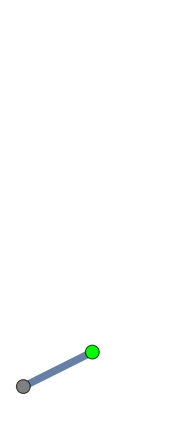
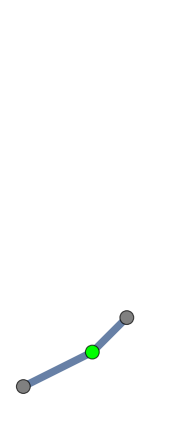
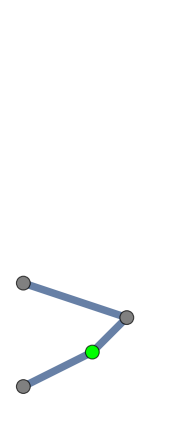
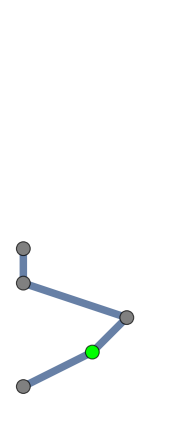
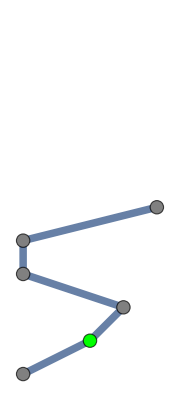
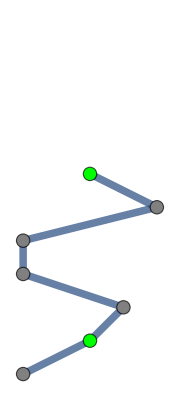
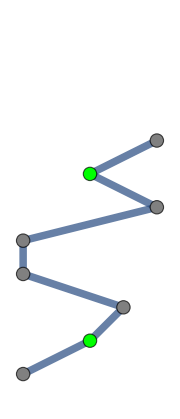
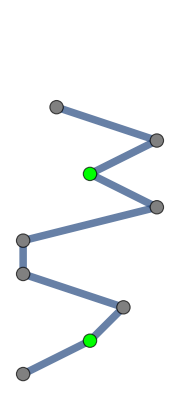

```mathematica
Final[Data,3]
```

```mathematica
#->Import["processedxx"<>StringPadLeft[ToString@#,2,"0"]<>".json","RawJSON"][[1]]["sendercount"]&/@Range[0,99]
```

Import::jsonkeynstr: Object keys must be strings.

Import::jsonhintposandchar: An error occurred near character '[', at line 10:3

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

{0→$Failed⟦1⟧[sendercount],1→3,2→5,3→4,4→3,5→5,6→4,7→1,8→4,9→4,10→1,11→2,12→5,13→2,14→2,15→2,16→5,17→3,18→3,19→5,20→3,21→5,22→1,23→4,24→5,25→2,26→1,27→3,28→3,29→5,30→4,31→3,32→3,33→3,34→1,35→2,36→3,37→5,38→3,39→3,40→3,41→2,42→5,43→1,44→1,45→3,46→3,47→5,48→2,49→2,50→5,51→2,52→4,53→3,54→2,55→4,56→4,57→5,58→2,59→2,60→2,61→5,62→5,63→1,64→5,65→3,66→4,67→2,68→1,69→3,70→1,71→4,72→4,73→1,74→2,75→1,76→2,77→2,78→1,79→5,80→2,81→3,82→3,83→2,84→2,85→5,86→1,87→4,88→4,89→1,90→2,91→3,92→2,93→3,94→2,95→1,96→5,97→1,98→1,99→3}

```mathematica
Manipulate[ListAnimate[Transpose[Final[Import["processedxx"<>StringPadLeft[ToString@index,2,"0"]<>".json","RawJSON"],#][[1;;-1]]&/@Range@ToExpression@Import["processedxx"<>StringPadLeft[ToString@index,2,"0"]<>".json","RawJSON"][[1]]["sendercount"]]],{index,1,99,1}]
```

```mathematica
Manipulate[Final[Import["processedxx"<>StringPadLeft[ToString@index,2,"0"]<>".json","RawJSON"],#][[-1]]&/@Range@ToExpression@Import["processedxx"<>StringPadLeft[ToString@index,2,"0"]<>".json","RawJSON"][[1]]["sendercount"],{index,1,99,1}]
```

```mathematica
(*Data=Import["axx_backup/processedxx03.json","RawJSON"];*)

Data=Import["processedxx02.json","RawJSON"];
Data[[1]]["sendercount"]
Transpose[Final[Data,#][[1;;-1]]&/@Range@ToExpression@1][[All,1]];
(*Export["gifs/async_messaging.gif",%]*)
(*Table[Export["gifs/simple_"<>ToString@i<>".pdf",%[[i]]],{i,Length@%}]*)
(*ListAnimate[Flatten@Transpose[Final[Data,#][[1;;-1]]&/@Range@ToExpression@1]]*)
ListAnimate[Transpose[Final[Data,#][[1;;-1]]&/@Range@ToExpression@Data[[1]]["sendercount"]]]
```

5

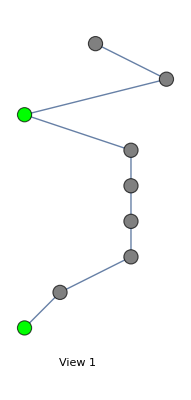

```mathematica
Show[
Graphics[Text[Style["View "<>ToString@1,Large],{1.5,0}]],
Graph[
Dut,
VertexCoordinates->Dyt,
EdgeShapeFunction->ef,
(*VertexLabels->Automatic,*)
(*VertexStyle->Red,*)
VertexShapeFunction-> CircleCurriedCheap[1,Length@Drt,Data[[5]]["clqs"][[1]],1,SuperCliques],
VertexSize->0.25,
EdgeStyle->Thick]]
```